```mathematica
δ[r_,a_,α_] = r^2+a^2 + r^4/(32 π α)(1-√(1+(128 π α)/r^3));
```

```mathematica
Limit[δ[r,a,α],α->0]
```

a^2+(-2+r) r

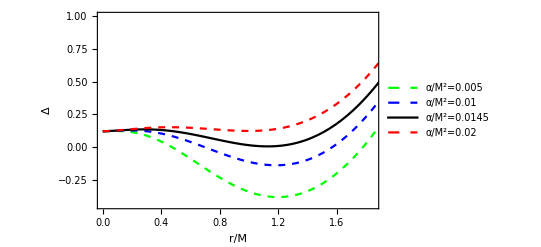

```mathematica
Plot[{δ[r,0.35,0.005],δ[r,0.35,0.01],δ[r,0.35,0.0145],δ[r,0.35,0.02]},{r,0,2},PlotStyle->{{Dashed,Green},{Dashed,Blue},Black,{Dashed,Red}},Frame->True,FrameLabel->{"r/M","Δ","a/M=0.35"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"α/M^2=0.005","α/M^2=0.01","α/M^2=0.0145","α/M^2=0.02"},{Scaled[{0.5,0.75}],{0.48,0.57}}],PlotRange->{{0,1.85},{-0.44,1}}]
```

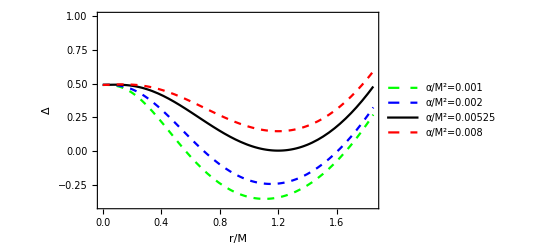

```mathematica
Plot[{δ[r,0.7,0.001],δ[r,0.7,0.002],δ[r,0.7,0.00525],δ[r,0.7,0.008]},{r,0,1.85},PlotStyle->{{Dashed,Green},{Dashed,Blue},Black,{Dashed,Red}},Frame->True,FrameLabel->{"r/M","Δ","a/M=0.7"},LabelStyle->{Black,Bold},PlotLegends->Placed[{"α/M^2=0.001","α/M^2=0.002","α/M^2=0.00525","α/M^2=0.008"},{Scaled[{0.65,0.75}],{0.5,0.5}}],PlotRange->{{0,1.85},{-0.4,1}}]
```

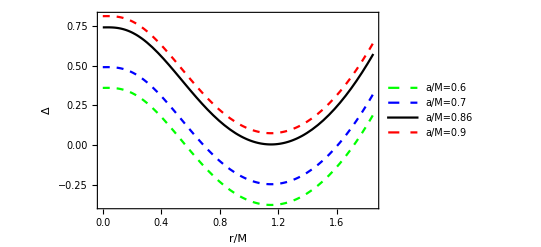

```mathematica
Plot[{δ[r,0.6,0.002],δ[r,0.7,0.002],δ[r,0.86,0.002],δ[r,0.9,0.002]},{r,0,1.85},PlotStyle->{{Dashed,Green},{Dashed,Blue},Black,{Dashed,Red}},Frame->True,FrameLabel->{"r/M","Δ","α/M^2= 0.002"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"a/M=0.6","a/M=0.7","a/M=0.86","a/M=0.9"},{Scaled[{0.65,0.75}],{0.5,0.5}}]]
```

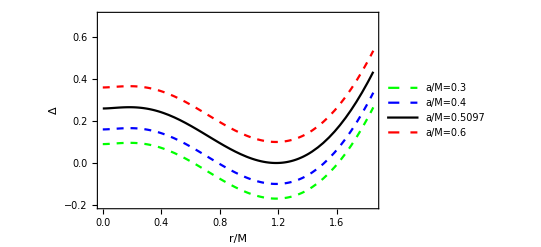

```mathematica
Plot[{δ[r,0.3,0.01],δ[r,0.4,0.01],δ[r,0.5097,0.01],δ[r,0.6,0.01]},{r,0,1.85},PlotStyle->{{Dashed,Green},{Dashed,Blue},Black,{Dashed,Red}},Frame->True,FrameLabel->{"r/M","Δ","α/M^2= 0.01"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0.3","a/M=0.4","a/M=0.5097","a/M=0.6"},{Scaled[{0.65,0.75}],{0.5,0.56}}],PlotRange->{{0,1.85},{-0.2,0.7}}]
```